```mathematica
SetDirectory[NotebookDirectory[]];
baseFilename="finalSolution-2025-05-18 12:53:35.870901322";
(*data=Import[StringForm[baseFilename <> ".csv",baseFilename], "Data"]; *)
data=Import[baseFilename <> ".csv", "Data"];
```

```mathematica
categorizedPoints = Style[{#[[1]],#[[2]]},If[#[[3]] < 0, Red, Blue]]& /@Select[data,#[[3]]<0&];
```

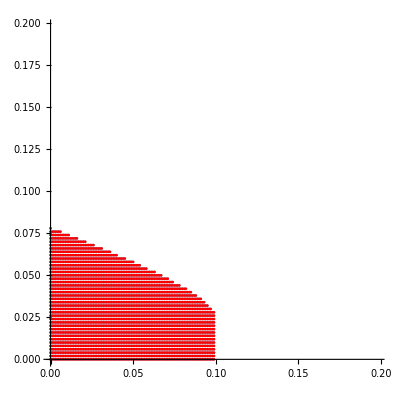

```mathematica
maxX=#[[1,1]]&/@categorizedPoints//Max;
maxY=#[[1,2]]&/@categorizedPoints//Max;
plot=ListPlot[categorizedPoints,PlotRange->{{0,2  Max[maxX,maxY]},{0,2   Max[maxX,maxY]}},AspectRatio->1]
```

```mathematica
Export[baseFilename <> ".png",plot]
```

finalSolution-2025-05-18 12:53:35.870901322.png

```mathematica
data[[1000]]
```

{0.002,0.178,-4.56876×10^-6}

```mathematica
categorizedPoints
```

{{0.,0.},{0.,0.002},{0.,0.004},{0.,0.006},{0.,0.008},{0.,0.01},2892,{0.099,0.02},{0.099,0.022},{0.099,0.024},{0.099,0.026},{0.099,0.028}}
 |  |  |  |

0.099

{{0.,0.},{0.,0.002},{0.,0.004},{0.,0.006},{0.,0.008},{0.,0.01},2892,{0.099,0.02},{0.099,0.022},{0.099,0.024},{0.099,0.026},{0.099,0.028}}
 |  |  |  |